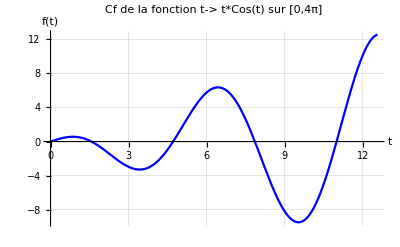

```mathematica
plot1=Plot[t*Cos[t],{t,0,4π},
(*Plotting options*)
AxesLabel->{"t","f(t)"},
PlotLabel->"Cf de la fonction t-> t*Cos(t) sur [0,4π]",
GridLines->Automatic,
PlotStyle->Blue]
```

# -Graphics-

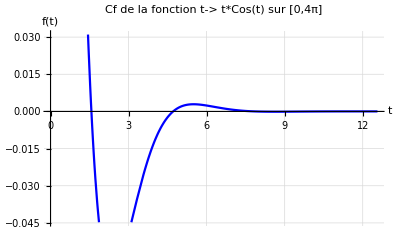

```mathematica
plot2=Plot[Exp[-t]*Cos[t],{t,0,4π},
(*Plotting options*)
AxesLabel->{"t","f(t)"},
PlotLabel->"Cf de la fonction t-> t*Cos(t) sur [0,4π]",
GridLines->Automatic,
PlotStyle->Blue]
```

```mathematica
(*soulution est PlotRange->all*)
```

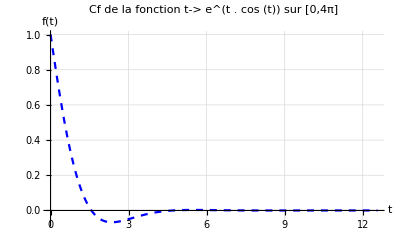

```mathematica
plot3=Plot[Exp[-t]*Cos[t],{t,0,4π},
(*Plotting options*)
AxesLabel->{"t","f(t)"},
PlotLabel->"Cf de la fonction t-> e^(t . cos (t)) sur [0,4π]",
GridLines->Automatic,
PlotStyle->{Blue,Dashed},(*-----*)
PlotRange->All]
```

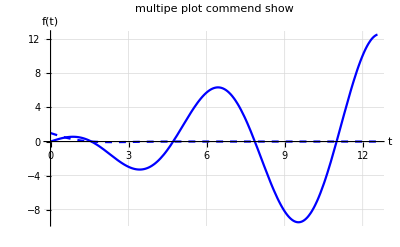

```mathematica
Show[plot1,plot3,
AxesLabel->{"t","f(t)"},
PlotLabel->"multipe plot commend show",
GridLines->Automatic,
PlotStyle->Blue]
(*monter les deux plot a meme fig*)
```

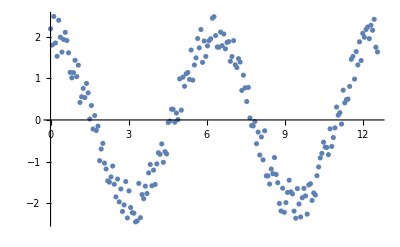

```mathematica
data=Table[{t,2Cos[t]+RandomReal[]-0.5},{t,0,4*Pi,2Pi/100}];
data//MatrixForm;
dataPlot=ListPlot[data]
```

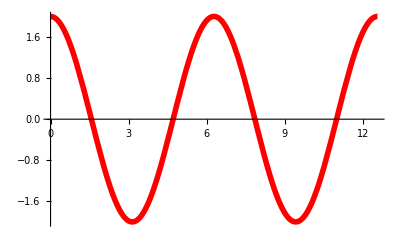

```mathematica
fitPlot=Plot[2Cos[t],{t,0,4π},PlotStyle->{Red,Thickness[0.01]}]
```

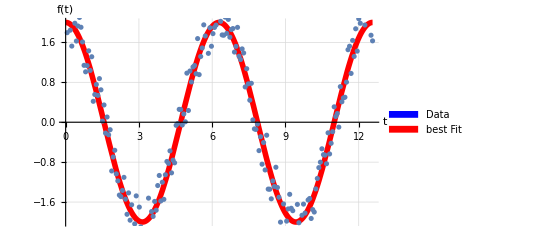

```mathematica
Legended[Show[fitPlot,dataPlot,
AxesLabel-> {"t","f(t)"},
GridLines->Automatic],
SwatchLegend[{Blue,Red},{"Data","best Fit"}]
]
```

```mathematica
Plo
```